```mathematica
NS["study_overlearningsimple1"]
```

```mathematica
label="testsimple2_50_1e+05.csv";scores=Flatten@Import["avgscores_"<>label];
lev=Flatten@Import["avglogev_"<>label];
pro=T@Import["avgprobs_"<>label];
surpr=Flatten@Import["avgsurprise_"<>label];
hit=Flatten@Import["avghit_"<>label];

sdscores=Flatten@Import["sdscores_"<>label];
sdlev=Flatten@Import["sdlogev_"<>label];
sdpro=Import["sdprobs_"<>label];
sdsurpr=Flatten@Import["sdsurprise_"<>label];
sdhit=Flatten@Import["sdhit_"<>label];

ffreqs=(#/Total@#)&@Flatten@Import["avgfreqs_"<>label];sdffreqs=(#/Total@#)&@Flatten@Import["sdfreqs_"<>label];
(*ffreqs=(#/Total/@#)&@Import["finalfreqs_"<>label];*)
ofreqs=Flatten@Import["targetfreqs_"<>label];
nsamples=Length@scores
```

50

```mathematica
nn=Sqrt[500];
```

```mathematica
{ofreqs,ffreqs}//N
```

{{0.5,0.5,0.},{0.499426,0.500574,0.}}

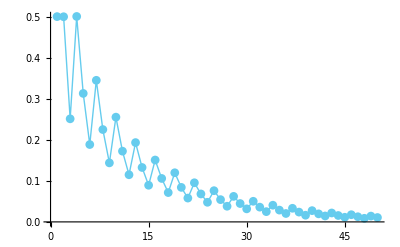

```mathematica
ListPlot[scores,Joined->True,PlotRange->All,PlotMarkers->Auto]
```

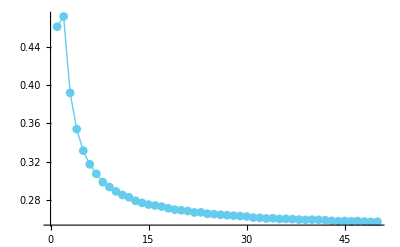

```mathematica
ListPlot[hit,Joined->True,PlotRange->All,PlotMarkers->Auto]
```

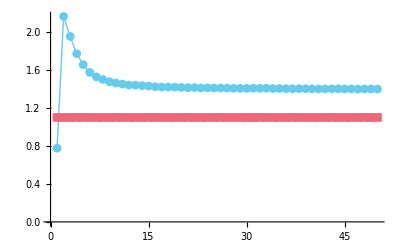

```mathematica
ListPlot[{surpr,-Table[Log@(1/3),{nsamples}]},GridLines->None,Joined->True,PlotRange->All,PlotMarkers->Auto]
```

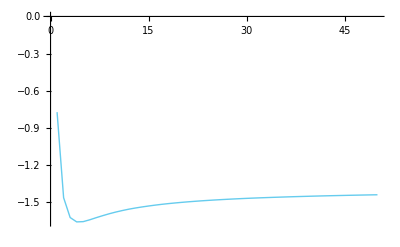

```mathematica
ListPlot[lev/Range@Length@lev,Joined->True,PlotRange->All]
```

```mathematica
(* define a parametric family for a 3-outcome space *)
```

```mathematica
expsum[t_]=Table[(1+KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/((1+ⅇ^t)^2),ⅇ^(2 t)/((1+ⅇ^t)^2),(2 ⅇ^t)/((1+ⅇ^t)^2)}

```mathematica
(* coords transfs to plot the two-distribution space *)
```

```mathematica
trmatrix=T[{{1,0},{0,0},{1/2,Sqrt[3]/2}}];proj[p_]:=trmatrix.p;

plotfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{PointSize@Large,red,Point[proj@nfreqs]}}]];
plotcfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{Thick,red,Circle[proj@nfreqs,0.02]}}]];
sp1={Black,Thin,Line[T[trmatrix][[{1,2,3,1}]]]};
```

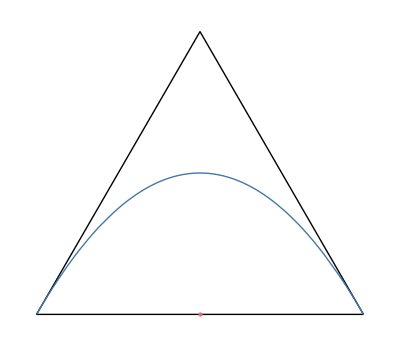

```mathematica
pplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];

doms={Graphics[{sp1}],pplot1};
Show[{doms,plotfreqs[ofreqs]},PlotRange->All]
```

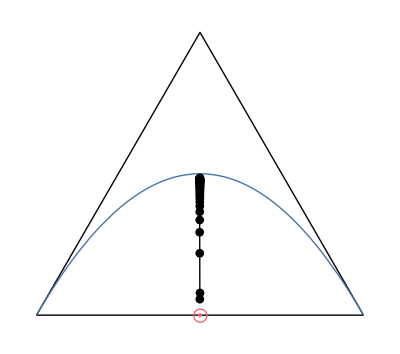

```mathematica
subrange=Round[Range[1,nsamples,nsamples/nsamples]];rplot1=ListPlot[Table[proj@pro[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{doms,plotfreqs@ofreqs,plotcfreqs@ffreqs,rplot1},PlotRange->All]
```

```mathematica
expdf0["overlearning2"]
```

overlearning2.pdf

```mathematica
gtest=Import["geommeantest.csv"];Dimensions[gtest]
```

{15,100000}

```mathematica
{mi=Min[gtest],ma=Max[gtest]}
```

{0.00739358,8.91574}

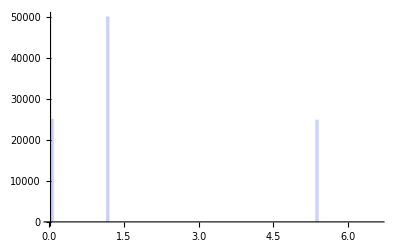

```mathematica
Histogram[gtest[[3,;;]],{mi,ma,(ma-mi)/100},PlotRange->All]
```

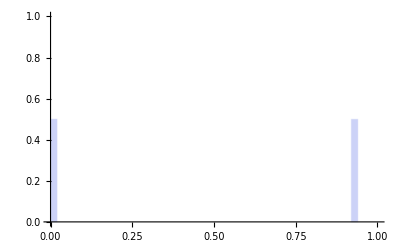

```mathematica
Histogram[Exp@-gtest[[2,;;]],{0,1,1/50},"Probability",PlotRange->{0,1}]
```

```mathematica
gtest[[10,1;;10]]
```

$Aborted[]

```mathematica
Table[{i,Mean@Exp@-gtest[[i,;;]],GeometricMean@Exp@-gtest[[i,;;]]},{i,15}]//MF
```

(1 | 0.46074 | 0.46074
2 | 0.471432 | 0.115266
3 | 0.391821 | 0.142216
4 | 0.354071 | 0.170416
5 | 0.331625 | 0.191455
6 | 0.317451 | 0.207567
7 | 0.307566 | 0.217627
8 | 0.298824 | 0.223526
9 | 0.293858 | 0.22899
10 | 0.28927 | 0.232218
11 | 0.285491 | 0.234665
12 | 0.283116 | 0.237196
13 | 0.279411 | 0.237281
14 | 0.277242 | 0.238566
15 | 0.275482 | 0.239712)